```mathematica
(*varList = {"50um367","75um374","100um373"};
functions = {};
tt = len+20*cyc; 
Do[
var = varList[[i]];
interpList = Import["F:\\mathematica_code\\data\\trail239_13high_26low_2newdmnp_40_240mm_size_shape_check-tcb2_80intensity_"<>var<>"_prompt_area.txt","Table"];
AppendTo[functions, Flatten[interpList]]
,{i,1,Length[varList]}
]*)
ClearAll[functions,varList,len,cyc,tt];
varList={"50um367","75um374","100um373"};
functions={};
len=550; (*Modify as needed*)
cyc=1; (*Modify as needed*)
tt=len+20*cyc;
Do[var=varList[[i]];
interpList=Import["/media/xlei45/Extreme Pro/mathematica_code/data/trail239_13high_26low_2newdmnp_40_240mm_size_shape_check-tcb2_80intensity_"<>var<>"_prompt_area.txt","Table"];
If[var=="100um373",interpList=Take[interpList,UpTo[len]]; (*Apply the selection only to "100um373"*)];
AppendTo[functions,Flatten[interpList]],{i,1,Length[varList]}]
```

{3}

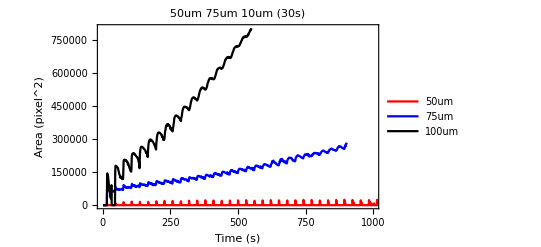

F:\mathematica_code\result\50um_75um_10um_30scycle.png

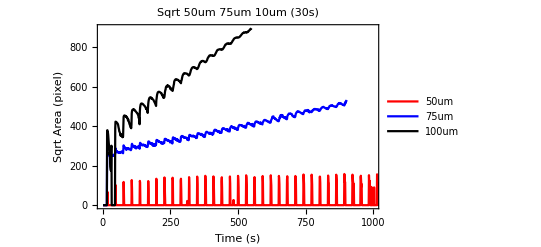

F:\mathematica_code\result\50um_75um_10um_30scycle_sqrt.png

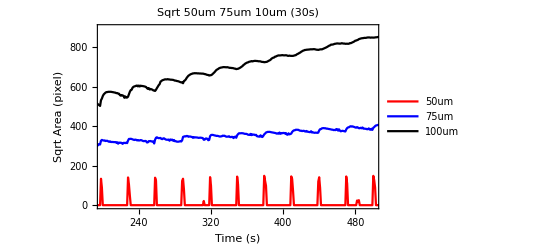

F:\mathematica_code\result\50um_75um_10um_30scycle_sqrt_rangechange.png

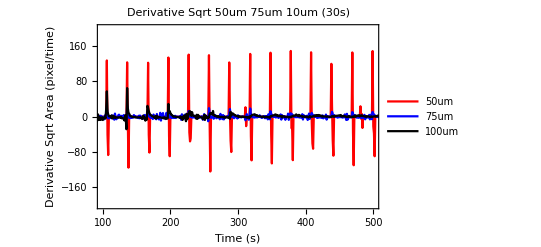

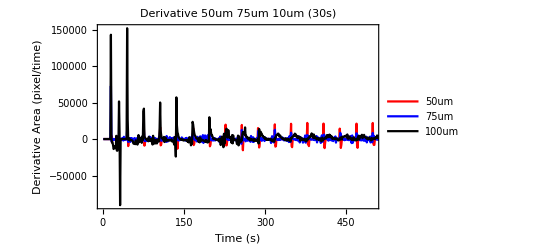

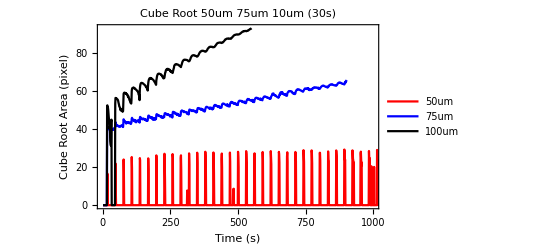

F:\mathematica_code\result\50um_75um_10um_30scycle_cuberoot.png

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}
];
Dimensions[functions]
plot=ListPlot[functions,Joined->True,FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotStyle->{Red,Blue,Black},PlotRange->{{0,1000},All},PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.7}],PlotLabel->"50um 75um 10um (30s) "]
Export["F:\\mathematica_code\\result\\50um_75um_10um_30scycle.png",plot]


functionsSqrt=Sqrt/@functions; (*apply the square root function to each element in functions*)
plotSqrt=ListPlot[functionsSqrt,Joined->True,FrameLabel->{"Time (s)","Sqrt Area (pixel)"},(*Change y axis label*)PlotStyle->{Red,Blue,Black},PlotRange->{{0,1000},All},PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.7}],PlotLabel->"Sqrt 50um 75um 10um (30s) "]

Export["F:\\mathematica_code\\result\\50um_75um_10um_30scycle_sqrt.png",plotSqrt]

plotSqrt=ListPlot[functionsSqrt,Joined->True,FrameLabel->{"Time (s)","Sqrt Area (pixel)"},(*Change y axis label*)PlotStyle->{Red,Blue,Black},PlotRange->{{200,500},All},PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.7}],PlotLabel->"Sqrt 50um 75um 10um (30s) "]

Export["F:\\mathematica_code\\result\\50um_75um_10um_30scycle_sqrt_rangechange.png",plotSqrt]

functionsSqrtDerivative=Differences/@functionsSqrt;
plotSqrtDerivative=ListPlot[functionsSqrtDerivative,Joined->True,FrameLabel->{"Time (s)","Derivative Sqrt Area (pixel/time)"},PlotStyle->{Red,Blue,Black},PlotRange->{{100,500},{-200,200}},PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.7}],PlotLabel->"Derivative Sqrt 50um 75um 10um (30s) "]

Export["F:\\mathematica_code\\result\\50um_75um_10um_30scycle_sqrt_derivative.png",plotSqrtDerivative];

functionsDerivative=Differences/@functions;
plotSqrtDerivative=ListPlot[functionsDerivative,Joined->True,FrameLabel->{"Time (s)","Derivative  Area (pixel/time)"},PlotStyle->{Red,Blue,Black},PlotRange-> {{0,500},All},PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.7}],PlotLabel->"Derivative 50um 75um 10um (30s) "]

Export["F:\\mathematica_code\\result\\50um_75um_10um_30scycle_derivative.png",plotSqrtDerivative];


functionsCubeRoot=CubeRoot/@#&/@functions; (*apply the cube root function to each element in functions*)

plotCubeRoot=ListPlot[functionsCubeRoot,Joined->True,FrameLabel->{"Time (s)","Cube Root Area (pixel)"},(*Change y axis label*)PlotStyle->{Red,Blue,Black},PlotRange->{{0,1000},All},PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.7}],PlotLabel->"Cube Root 50um 75um 10um (30s) "]

Export["F:\\mathematica_code\\result\\50um_75um_10um_30scycle_cuberoot.png",plotCubeRoot]
```

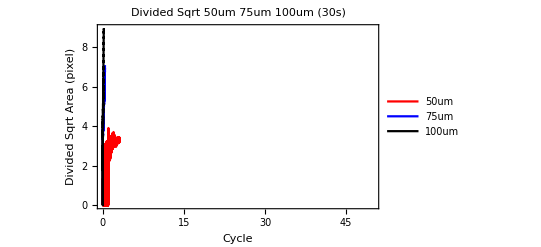

```mathematica
cycleTime = 30; (*length of a cycle in seconds*)
dividers = {50, 75, 100}; (*your dividers*)

functionsSqrt = Sqrt /@ functions; 

(* Here's the corrected transformation, now it divides the actual time by cycleTime *)
transformedFunctionsSqrt = MapIndexed[{#2[[1]]/cycleTime, #1} &, #] & /@ functionsSqrt;

(*divide each transformed function by corresponding divider*)
dividedTransformedFunctionsSqrt = MapThread[#1/#2 &, {transformedFunctionsSqrt, dividers}];

SetOptions[ListPlot, Frame -> True, Axes -> False, 
  FrameTicksStyle -> Thickness[.001], 
  FrameStyle -> Directive[Black, Thickness[0.001]], 
  LabelStyle -> {FontFamily -> "Arial", Black, FontSize -> 16}];

plotDividedSqrt = 
  ListPlot[dividedTransformedFunctionsSqrt, Joined -> True, 
    FrameLabel -> {"Cycle", "Divided Sqrt Area (pixel)"}, 
    PlotStyle -> {Red, Blue, Black}, PlotRange -> {{0, 50}, All}, 
    PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.7}], 
    PlotLabel -> "Divided Sqrt 50um 75um 100um (30s) "]

Export["F:\\mathematica_code\\result\\50um_75um_100um_30scycle_divided_sqrt.png", plotDividedSqrt];
```

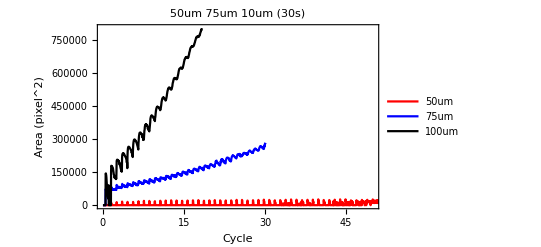

F:\mathematica_code\result\50um_75um_10um_30scycle.png

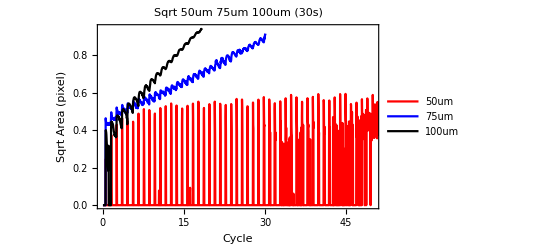

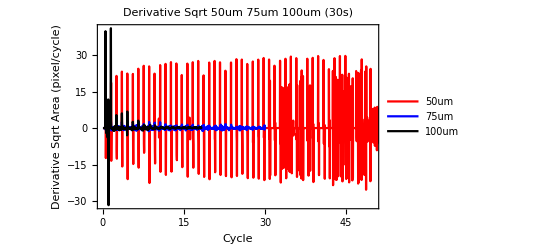

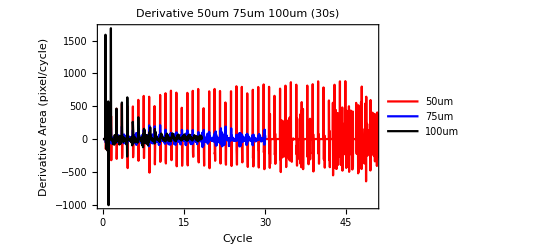

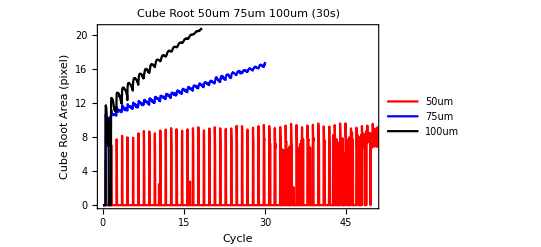

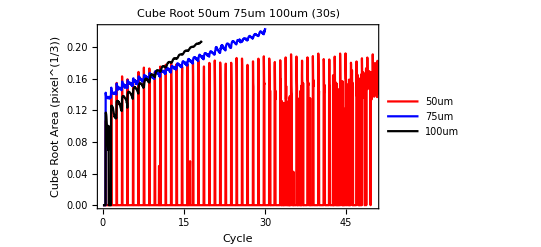

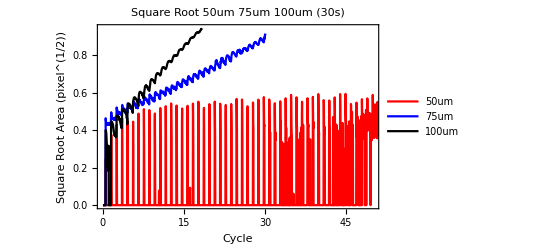

F:\mathematica_code\result\50um_75um_100um_30scycle_sqrt.png

```mathematica
cycleTime=30; (*length of a cycle in seconds*)

transformedFunctions=MapIndexed[{First[#2]/cycleTime,#1}&,#]&/@functions;

SetOptions[ListPlot,Frame->True,Axes->False,FrameTicksStyle->Thickness[.001],FrameStyle->Directive[Black,Thickness[0.001]],LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

(*Plot normal function*)plot=ListPlot[transformedFunctions,Joined->True,FrameLabel->{"Cycle"," Area (pixel^2)"},PlotStyle->{Red,Blue,Black},PlotRange->{{0,50},All},(*Modify this line to limit x-axis range*)PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.7}],PlotLabel->"50um 75um 10um (30s) "]
Export["F:\\mathematica_code\\result\\50um_75um_10um_30scycle.png",plot]

(*Apply the same modification to other plots*)
(*Rest of your code here,replacing'PlotRange->{{0,1000},All}' with'PlotRange->{{0,50},All}'*)

(*
functionsCycle=MapIndexed[#1/(30*First[#2])&,functions];
functionsCycleSqrt=Sqrt/@functionsCycle;
functionsCycleSqrtDerivative=Differences/@functionsCycleSqrt;
functionsCycleDerivative=Differences/@functionsCycle;
functionsCycleCubeRoot=CubeRoot/@functionsCycle;

transformedFunctionsSqrtCycle =  MapIndexed[{First[#2]/cycleTime, #1} &, #] & /@ functionsSqrtCycle;*)
(*transformedfunctionsCycleSqrtDerivative =  MapIndexed[{First[#2]/cycleTime, #1} &, #] & /@ functionsCycleSqrtDerivative;
transformedfunctionsCycleDerivative =  MapIndexed[{First[#2]/cycleTime, #1} &, #] & /@ functionsCycleDerivative;
transformedfunctionsCycleCubeRoot =  MapIndexed[{First[#2]/cycleTime, #1} &, #] & /@ functionsCycleCubeRoot;*)

plotSqrtCycle = 
 ListPlot[transformedFunctionsSqrtCycle, Joined -> True, 
  FrameLabel -> {"Cycle", "Sqrt Area (pixel)"}, 
  PlotStyle -> {Red, Blue, Black}, PlotRange -> {{0, 50}, All}, 
  PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.7}], 
  PlotLabel -> "Sqrt 50um 75um 100um (30s) "]
Export["F:\\mathematica_code\\result\\50um_75um_100um_30scycle_sqrt_\

cycle.png", plotSqrtCycle];


cycleTime = 30; (*length of a cycle in seconds*)
dividers = {50, 75, 100}; (*your dividers*)

functionsSqrt = Sqrt /@ functions; 
transformedFunctionsSqrt = MapIndexed[{First[#2]/cycleTime, #1} &, #] & /@ functionsSqrt;

(*divide each transformed function by corresponding divider*)
dividedTransformedFunctionsSqrt = MapThread[#1/#2 &, {transformedFunctionsSqrt, dividers}];

SetOptions[ListPlot, Frame -> True, Axes -> False, 
  FrameTicksStyle -> Thickness[.001], 
  FrameStyle -> Directive[Black, Thickness[0.001]], 
  LabelStyle -> {FontFamily -> "Arial", Black, FontSize -> 16}];





plotSqrtCycle = 
 ListPlot[transformedfunctionsCycleSqrtDerivative, Joined -> True, 
  FrameLabel -> {"Cycle", "Derivative Sqrt Area (pixel/cycle)"}, 
  PlotStyle -> {Red, Blue, Black}, PlotRange -> {{0, 50}, All}, 
  PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.7}], 
  PlotLabel -> "Derivative Sqrt 50um 75um 100um (30s) "]
Export["F:\\mathematica_code\\result\\50um_75um_100um_30scycle_\

derivative_sqrt_cycle.png", plotSqrtDerivativeCycle];

plotSqrtCycle = 
 ListPlot[transformedfunctionsCycleDerivative, Joined -> True, 
  FrameLabel -> {"Cycle", "Derivative Area (pixel/cycle)"}, 
  PlotStyle -> {Red, Blue, Black}, PlotRange -> {{0, 50}, All}, 
  PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.7}], 
  PlotLabel -> "Derivative 50um 75um 100um (30s) "]
Export["F:\\mathematica_code\\result\\50um_75um_100um_30scycle_\

derivative_cycle.png", plotDerivativeCycle];

plotSqrtCycle = 
 ListPlot[transformedfunctionsCycleCubeRoot, Joined -> True, 
  FrameLabel -> {"Cycle", "Cube Root Area (pixel)"}, 
  PlotStyle -> {Red, Blue, Black}, PlotRange -> {{0, 50}, All}, 
  PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.7}], 
  PlotLabel -> "Cube Root 50um 75um 100um (30s) "]
Export["F:\\mathematica_code\\result\\50um_75um_100um_30scycle_\

cuberoot_cycle.png", plotCubeRootCycle];

cycleTime = 30; (*length of a cycle in seconds*)
dividers = {50, 75, 100}; (*your dividers*)

functionsCycle = MapIndexed[#1/(cycleTime*First[#2]) &, functions];
functionsCycleCubeRoot = CubeRoot /@ functionsCycle;

(*divide each function by corresponding divider*)
dividedFunctionsCubeRootCycle = MapThread[#1/#2 &, {functionsCycleCubeRoot, dividers}];

transformedFunctionsCubeRootCycle =  
  MapIndexed[{First[#2]/cycleTime, #1} &, #] & /@ dividedFunctionsCubeRootCycle;

plotCubeRootCycle = 
  ListPlot[transformedFunctionsCubeRootCycle, Joined -> True, 
    FrameLabel -> {"Cycle", "Cube Root Area (pixel^(1/3))"}, 
    PlotStyle -> {Red, Blue, Black}, PlotRange -> {{0, 50}, All}, 
    PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.7}], 
    PlotLabel -> "Cube Root 50um 75um 100um (30s) "]
Export["F:\\mathematica_code\\result\\50um_75um_100um_30scycle_cuberoot_cycle.png", plotCubeRootCycle];



cycleTime = 30; (*length of a cycle in seconds*)
dividers = {50, 75, 100}; (*your dividers*)

functionsCycle = MapIndexed[#1/(cycleTime*First[#2]) &, functions];
functionsCycleSqrt = 
  Sqrt /@ functionsCycle; (*Replace CubeRoot with Sqrt*)

(*divide each function by corresponding divider*)
dividedFunctionsSqrtCycle = 
  MapThread[#1/#2 &, {functionsCycleSqrt, dividers}];

transformedFunctionsSqrtCycle =  
    MapIndexed[{First[#2]/cycleTime, #1} &, #] & /@ 
   dividedFunctionsSqrtCycle;

plotSqrtCycle = 
   ListPlot[transformedFunctionsSqrtCycle, Joined -> True, 
      FrameLabel -> {"Cycle", 
    "Square Root Area (pixel^(1/2))"},  (*Change label*)
      PlotStyle -> {Red, Blue, Black}, PlotRange -> {{0, 50}, All}, 
      PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.7}], 
      PlotLabel -> 
   "Square Root 50um 75um 100um (30s) "] (*Change label*)
Export["/media/xlei45/Extreme Pro/mathematica_code/result/50um_75um_100um_30scycle_sqrt_cycle.png", plotSqrtCycle]; (*Change filename*)
```

{/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse/50um_100intensity_tcb2_3ul_32mgml_1ul_nitrophen20_prompt_area.txt,/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse/50um_100intensity_tcb2_3ul_32mgml_1ul_nitrophen22_prompt_area.txt,/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse/50um_100intensity_tcb2_3ul_32mgml_1ul_nitrophen23_prompt_area.txt}

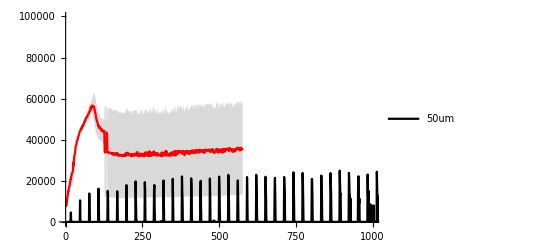

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16},
PlotStyle->{Black,Yellow,Cyan,Red,Green,Blue,Magenta,Orange},
PlotRange->{{0,600},{0,100000}},PlotLegends->Automatic,FrameLabel->{"Time (s)"," Area (pixel^2)"}
];

folder="/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
files=FileNames["50um*tcb2_3ul*1ul*.txt",folder];
data=ReadList[#,Number]&/@files;
files
syncData=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files);(*Remove empty lists*)
syncData=DeleteCases[syncData,{}];
selectedSyncData=syncData[[{1,2,3}]];


(*ListPlot[data,Joined->True,PlotLabel->"rawData",PlotLegends->Automatic]
ListPlot[syncData,Joined->True,PlotLabel->"syncData",PlotLegends->Automatic]
ListPlot[selectedSyncData,Joined->True,PlotLabel->"SelectedSyncData"]
*)

data={selectedSyncData[[1]],selectedSyncData[[2]],selectedSyncData[[3]]};
minLength=Min[Length/@data];
truncatedData=Take[#,minLength]&/@data;
meanData=Mean/@Transpose[truncatedData];
stdData=StandardDeviation/@Transpose[truncatedData];
upper=meanData+stdData;
lower=meanData-stdData;

(*ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Black,None},FillingStyle->LightGray,PlotLabel->"syncDataErrorBar",FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotRange->{{0,600},{0,100000}}]*)

plot1=ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Red,None},FillingStyle->LightGray,FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotRange->{{0,1000},{0,100000}}];
plot2=ListPlot[functions[[1]],Joined->True,FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotStyle->{Black},PlotRange->{{0,1000},All},PlotLegends->Placed[{"50um","75um","100um"},{0.8,0.8}]];
Show[plot1,plot2]
```

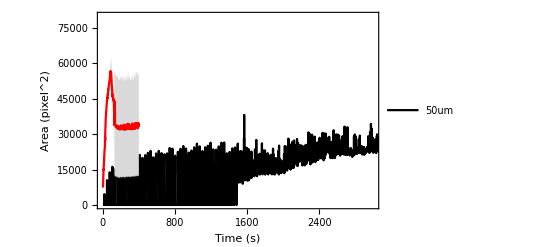

-Graphics-

//media/xlei45/Extreme Pro/mathematica_code/result/combinedPlot_3.png

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
files = FileNames["50um*tcb2_3ul*1ul*.txt", folder];
data = ReadList[#, Number] & /@ files;

syncData = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);(*Remove empty lists*)
syncData = DeleteCases[syncData, {}];
selectedSyncData = syncData[[{1, 2, 3}]];

data = {selectedSyncData[[1]], selectedSyncData[[2]], selectedSyncData[[3]]};
minLength = Min[Length /@ data];
truncatedData = Take[#, minLength] & /@ data;

(* Restrict the computations to the first 100 data points *)
truncatedData = Take[#, 400] & /@ truncatedData;
meanData = Mean /@ Transpose[truncatedData];
stdData = StandardDeviation /@ Transpose[truncatedData];
upper = meanData + stdData;
lower = meanData - stdData;

plot1 = ListLinePlot[{lower, meanData, upper}, Filling -> {1 -> {3}}, 
   PlotStyle -> {None, Red, None}, FillingStyle -> LightGray, 
   FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
   PlotRange -> All];  (* Let Mathematica determine the range *)
plot2 = ListPlot[functions[[1]], Joined -> True, 
   FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
   PlotStyle -> {Black}, PlotRange -> {{0, 3000}, {0,80000}},
   PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.8}]];
Show[plot2, plot1]
combinedPlot = Show[plot2, plot1]

(* Export the figure *)
Export["//media/xlei45/Extreme Pro/mathematica_code/result/combinedPlot_3.png", combinedPlot]
```

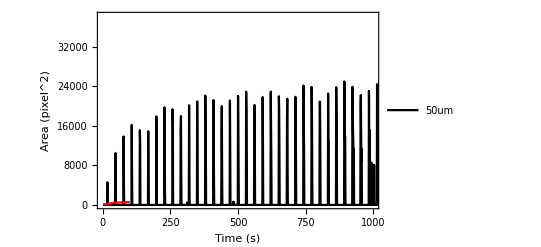

//media/xlei45/Extreme Pro/mathematica_code/result/combinedPlot.png

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
files = FileNames["50um*tcb2_3ul*1ul*.txt", folder];
data = ReadList[#, Number] & /@ files;
syncData = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);(*Remove empty lists*)
syncData = DeleteCases[syncData, {}];
selectedSyncData = syncData[[{1, 2, 3}]];

data = {selectedSyncData[[1]], selectedSyncData[[2]], selectedSyncData[[3]]};
minLength = Min[Length /@ data];
truncatedData = Take[#, minLength] & /@ data;

(* Restrict the computations to the first 100 data points *)
truncatedData = Take[#, 100] & /@ truncatedData;

(* Divide the data by 100 *)
dividedData = #/100 & /@ truncatedData;

meanData = Mean /@ Transpose[dividedData];
stdData = StandardDeviation /@ Transpose[dividedData];
upper = meanData + stdData;
lower = meanData - stdData;

plot1 = ListLinePlot[{lower, meanData, upper}, Filling -> {1 -> {3}}, 
   PlotStyle -> {None, Red, None}, FillingStyle -> LightGray, 
   FrameLabel -> {"Time (s)", " Area (pixel^2)/100"}, 
   PlotRange -> All];  (* Let Mathematica determine the range *)

plot2 = ListPlot[functions[[1]], Joined -> True, 
   FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
   PlotStyle -> {Black}, PlotRange -> {{0, 1000}, All},
   PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.8}]];

combinedPlot = Show[plot2, plot1]

(* Export the figure *)
Export["//media/xlei45/Extreme Pro/mathematica_code/result/combinedPlot.png", combinedPlot]
```

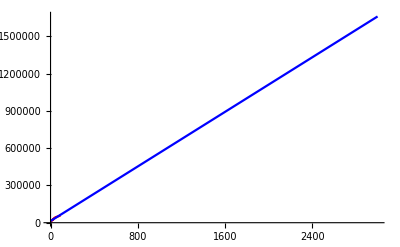

```mathematica
(* Let's suppose meanData represents your y values and time represents your x values *)
time = Range[0, Length[meanData] - 1];

(* Fit the data to a linear model *)
linearModel = Fit[Transpose[{time, meanData}], {1, x}, x];

(* Define a function based on the obtained model *)
linearFunction[x_] = linearModel;

(* Generate extrapolated data for the range 0-1000 *)
extrapolatedTime = Range[0, 3000];
extrapolatedData = linearFunction /@ extrapolatedTime;

(* Plot the extrapolated data along with the original data *)
plot1Extrapolated = ListLinePlot[extrapolatedData, PlotStyle -> {Blue}, PlotRange -> {{0, 1000}, All}];
Show[plot1, plot1Extrapolated, PlotRange -> {{0, 3000}, All}]
```

Part::take: Cannot take positions 1 through 100 in {0,1,2,3,4,5,6,7,8,9,«80»}.

Part::take: Cannot take positions 1 through 100 in {7372.67,7804.,8665.33,9616.17,11267.7,12238.,13018.7,15112.5,14858.,15935.3,«80»}.

Part::take: Cannot take positions 1 through 100 in {0,1,2,3,4,5,6,7,8,9,«80»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 100 in {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,«80»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

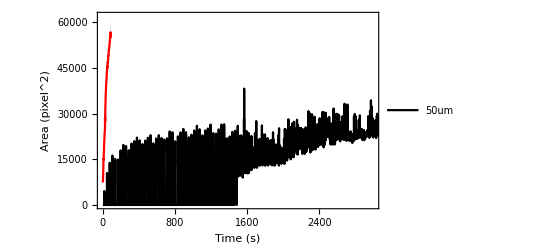

```mathematica
(* Let's suppose meanData represents your y values and time represents your x values *)
time = Range[0, Length[meanData] - 1];

(* Fit the first 100 data points to a linear model *)
linearModel = Fit[Transpose[{time[[1 ;; 100]], meanData[[1 ;; 100]]}], {1, x}, x];

(* Define a function based on the obtained model *)
linearFunction[x_] = linearModel;

(* Generate extrapolated data for the range 0-1000 *)
extrapolatedTime = Range[0, 3000];
extrapolatedData = linearFunction /@ extrapolatedTime;

(* Generate plot for the extrapolated data *)
plot1Extrapolated = ListLinePlot[extrapolatedData, PlotStyle -> {Blue}, PlotRange -> {{0, 1000}, All}];

(* Plot the original meanData with error bounds *)
plot1 = ListLinePlot[{lower, meanData, upper}, Filling -> {1 -> {3}}, 
      PlotStyle -> {None, Red, None}, FillingStyle -> LightGray, 
      FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
      PlotRange -> {{0, 100}, All}]; 

(* Generate plot for the functions data *)
plot2 = ListPlot[functions[[1]], Joined -> True, 
      FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
      PlotStyle -> {Black}, PlotRange -> {{0, 1000}, All},
      PlotLegends -> Placed[{"50um", "75um", "100um"}, {0.8, 0.8}]];

(* Show the extrapolated plot with the original data *)
Show[plot2, plot1, plot1Extrapolated, PlotRange -> {{0, 3000}, All}]
```

## 75um

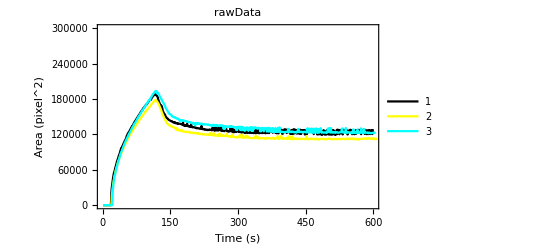

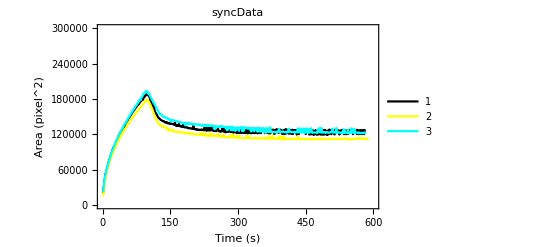

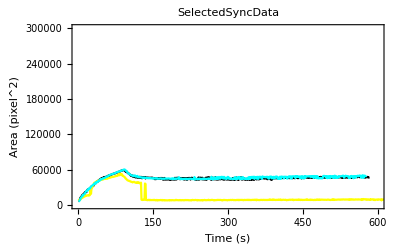

{}

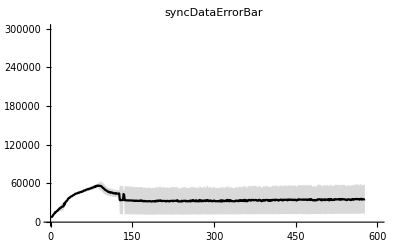

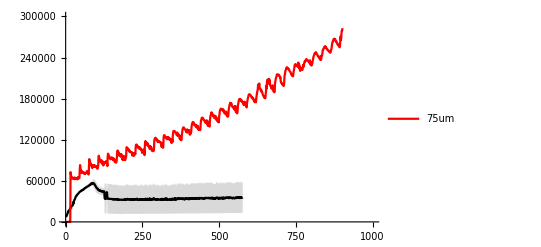

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16},
PlotStyle->{Black,Yellow,Cyan,Red,Green,Blue,Magenta,Orange},
PlotRange->{{0,600},{0,300000}},
PlotLegends->Automatic,FrameLabel->{"Time (s)"," Area (pixel^2)"}
];


selectedSyncData=syncData[[{1,2,3}]];  

folder="/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
files=FileNames["75um*3ul*.txt",folder];
data=ReadList[#,Number]&/@files;
syncData=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files);(*Remove empty lists*)
syncData=DeleteCases[syncData,{}];



ListPlot[data,Joined->True,PlotLabel->"rawData", PlotLegends->Automatic]
ListPlot[syncData,Joined->True,PlotLabel->"syncData",PlotLegends->Automatic]
ListPlot[selectedSyncData,Joined->True,PlotLabel->"SelectedSyncData"]
Dimensions[selectedData]

data={selectedSyncData[[1]],selectedSyncData[[2]],selectedSyncData[[3]]};
minLength=Min[Length/@data];
truncatedData=Take[#,minLength]&/@data;
meanData=Mean/@Transpose[truncatedData];
stdData=StandardDeviation/@Transpose[truncatedData];
upper=meanData+stdData;
lower=meanData-stdData;

ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Black,None},FillingStyle->LightGray,PlotLabel->"syncDataErrorBar",FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotRange->{{0,600},{0,300000}}]

plot1=ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Black,None},FillingStyle->LightGray,FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotRange->{{0,1000},{0,300000}}];

plot2=ListPlot[functions[[2]],Joined->True,FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotStyle->{Red},PlotRange->{{0,1000},All},PlotLegends->Placed[{"75um","100um"},{0.8,0.8}]];

Show[plot1,plot2]
```

## 100um

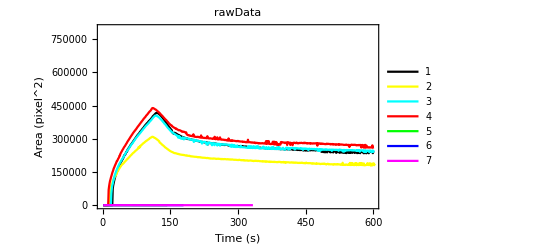

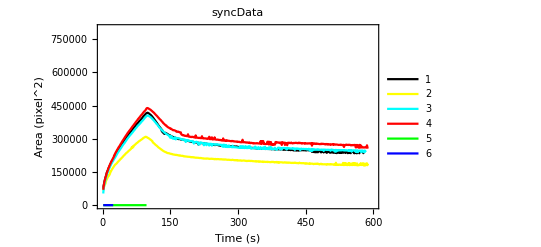

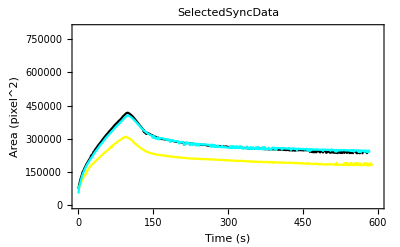

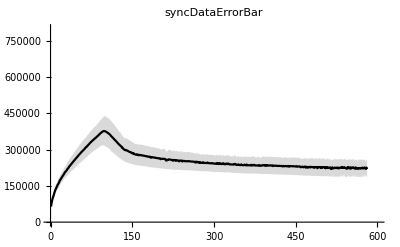

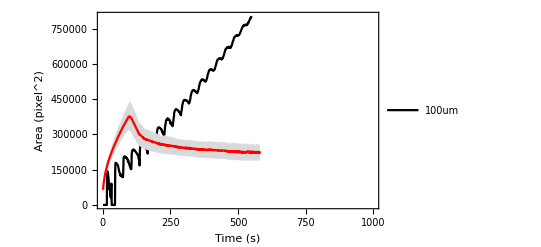

//media/xlei45/Extreme Pro/mathematica_code/result/combinedPlot_2.png

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.001]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16},
PlotStyle->{Black,Yellow,Cyan,Red,Green,Blue,Magenta,Orange},
PlotRange->{{0,600},{0,800000}},
PlotLegends->Automatic,FrameLabel->{"Time (s)"," Area (pixel^2)"}
];




folder="/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
files=FileNames["100um*3ul*.txt",folder];
data=ReadList[#,Number]&/@files;
syncData=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files);(*Remove empty lists*)
syncData=DeleteCases[syncData,{}];


ListPlot[data,Joined->True,PlotLabel->"rawData", PlotLegends->Automatic]
ListPlot[syncData,Joined->True,PlotLabel->"syncData",PlotLegends->Automatic]
ListPlot[selectedSyncData,Joined->True,PlotLabel->"SelectedSyncData"]

selectedSyncData=syncData[[{1,2,3}]];  
data={selectedSyncData[[1]],selectedSyncData[[2]],selectedSyncData[[3]]};
minLength=Min[Length/@data];
truncatedData=Take[#,minLength]&/@data;
meanData=Mean/@Transpose[truncatedData];
stdData=StandardDeviation/@Transpose[truncatedData];
upper=meanData+stdData;
lower=meanData-stdData;

ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Black,None},FillingStyle->LightGray,PlotLabel->"syncDataErrorBar",FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotRange->{{0,600},{0,800000}}]

plot1=ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Red,None},FillingStyle->LightGray,FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotRange->{{0,1000},{0,800000}}];

plot2=ListPlot[functions[[3]],Joined->True,FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotStyle->{Black},PlotRange->{{0,1000},All},PlotLegends->Placed[{"100um"},{0.8,0.8}]];

combinedPlot = Show[plot2, plot1]

(* Export the figure *)
Export["//media/xlei45/Extreme Pro/mathematica_code/result/combinedPlot_2.png", combinedPlot]
```

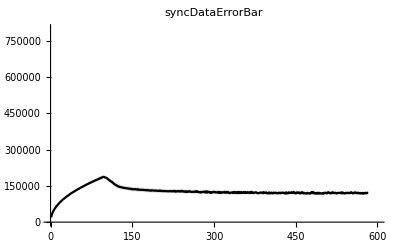

-Graphics-

## color_changed bar

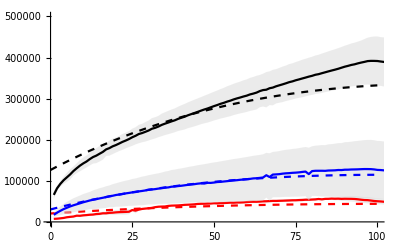

/media/xlei45/Extreme Pro/mathematica_code/result/50um75um100umLongTerm.png

{20486.6+530.311 x-3.83473 x^2+0.00955404 x^3-7.72854×10^-6 x^4,30313.8+2045.77 x-16.3621 x^2+0.0482006 x^3-0.0000477758 x^4,126426.+4210.18 x-27.3498 x^2+0.0632237 x^3-0.0000486558 x^4}

```mathematica
(*folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";
filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
plots = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, Transparent, Transparent, Black, Transparent}; (* List of colors *)

i = 1;
Do[
 files = FileNames[pattern, folder];
 data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
 data = DeleteCases[data, {}];
 minLength = Min[Length /@ data];
 truncatedData = Take[#, minLength] & /@ data;
 meanData = Mean /@ Transpose[truncatedData];
 stdData = StandardDeviation /@ Transpose[truncatedData];
 upper = meanData + stdData;
 lower = meanData - stdData;
 plot = ListLinePlot[{lower, meanData, upper}, 
     Filling -> {1 -> {3}}, 
     PlotStyle -> {colors[[i]], colors[[i+1]], colors[[i+2]]}, (* Change color based on iteration *)
     FillingStyle -> Directive[Opacity[0.5], LightGray], 
     PlotLabel -> "50um75um100umLongTerm", 
     FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
     PlotRange -> {{0, 100}, {0, 500000}}];
 AppendTo[plots, plot];
 i = i + 3;, {pattern, filePatterns}] (* Increment i by 3 at each iteration *)

Show[plots]
Export[FileNameJoin[{resultFolder, "50um75um100umLongTerm.png"}], plots]*)

folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";
filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
plots = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, 
   Transparent, Transparent, Black, Transparent}; (* List of colors *)
equations = {};

i = 1;
Do[
  files = FileNames[pattern, folder];
  data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
  data = DeleteCases[data, {}];
  minLength = Min[Length /@ data];
  truncatedData = Take[#, minLength] & /@ data;
  meanData = Mean /@ Transpose[truncatedData];
  stdData = StandardDeviation /@ Transpose[truncatedData];
  upper = meanData + stdData;
  lower = meanData - stdData;
  (* fit a fourth degree polynomial model *)
  fit = Fit[meanData, {1, x, x^2, x^3, x^4}, x];
  (* keep the equation *)
  AppendTo[equations, fit];
  (* create plots for both the data and the fit *)
  plotData = ListLinePlot[{lower, meanData, upper}, 
        Filling -> {1 -> {3}}, 
        PlotStyle -> {colors[[i]], colors[[i + 1]], colors[[i + 2]]}, 
        FillingStyle -> Directive[Opacity[0.5], LightGray], 
        FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
        PlotRange -> {{0, 100}, {0, 500000}}];
  plotFit = Plot[fit, {x, 0, 100}, PlotStyle -> {colors[[i + 1]], Dashed}];
  (* append both plots to the list of plots *)
  AppendTo[plots, plotData];
  AppendTo[plots, plotFit];
  i = i + 3;,
 {pattern, filePatterns}] 

Show[plots]
Export[FileNameJoin[{resultFolder, "50um75um100umLongTerm.png"}], plots]

Print[equations]
```

```mathematica
"F:\\mathematica_code\\data\\result\\50um75um100umLongTerm.png"
```

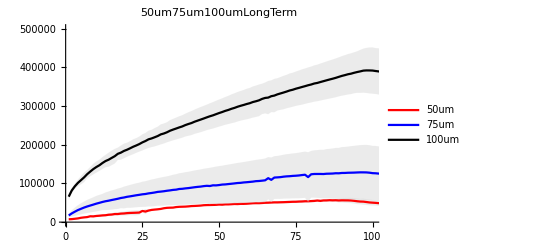

/media/xlei45/Extreme Pro/mathematica_code/result/50um75um100umLongTerm.png

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";
filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
legends = {"50um", "75um", "100um"};
plots = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, Transparent, Transparent, Black, Transparent}; (* List of colors *)

i = 1;
Do[
 files = FileNames[pattern, folder];
 data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
 data = DeleteCases[data, {}];
 minLength = Min[Length /@ data];
 truncatedData = Take[#, minLength] & /@ data;
 meanData = Mean /@ Transpose[truncatedData];
 stdData = StandardDeviation /@ Transpose[truncatedData];
 upper = meanData + stdData;
 lower = meanData - stdData;
 plot = ListLinePlot[{lower, meanData, upper}, 
     Filling -> {1 -> {3}}, 
     PlotStyle -> {colors[[i]], colors[[i+1]], colors[[i+2]]}, (* Change color based on iteration *)
     FillingStyle -> Directive[Opacity[0.5], LightGray], 
     PlotLabel -> "50um75um100umLongTerm", 
     FrameLabel -> {"Time (s)", " Area (pixel^2)"}, 
     PlotRange -> {{0, 100}, {0, 500000}}];
 AppendTo[plots, plot];
 i = i + 3;, {pattern, filePatterns}] (* Increment i by 3 at each iteration *)

(* Create a combined plot with manually placed legend *)
combinedPlot = Legended[
    Show[plots],
    Placed[LineLegend[{Red, Blue, Black}, legends], Right]
]

Export[FileNameJoin[{resultFolder, "50um75um100umLongTerm.png"}], combinedPlot] (* Export the plot with the legends *)
```

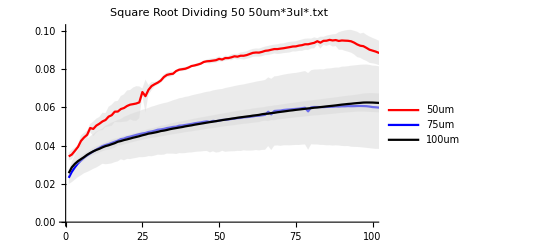

```mathematica
Show[%1436,Background->White]
```

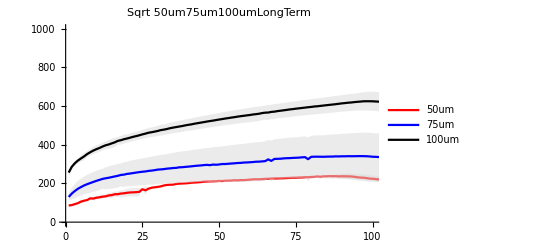

/media/xlei45/Extreme Pro/mathematica_code/result/sqrt50um75um100umLongTerm.png

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";

filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
legends = {"50um", "75um", "100um"};
plots = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, Transparent, Transparent, Black, Transparent}; (* List of colors *)

i = 1;
Do[
 files = FileNames[pattern, folder];
 data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
 data = DeleteCases[data, {}];
 minLength = Min[Length /@ data];
 truncatedData = Take[#, minLength] & /@ data;
 sqrtTruncatedData = Sqrt /@ truncatedData;
 meanData = Mean /@ Transpose[sqrtTruncatedData];
 stdData = StandardDeviation /@ Transpose[sqrtTruncatedData];
 upper = meanData + stdData;
 lower = meanData - stdData;
 plot = ListLinePlot[{lower, meanData, upper}, 
     Filling -> {1 -> {3}}, 
     PlotStyle -> {colors[[i]], colors[[i+1]], colors[[i+2]]}, (* Change color based on iteration *)
     FillingStyle -> Directive[Opacity[0.5], LightGray], 
     PlotLabel -> "Sqrt 50um75um100umLongTerm", 
     FrameLabel -> {"Time (s)", " Sqrt Area (pixel)"}, 
     PlotRange -> {{0, 100}, {0, 1000}}];
 AppendTo[plots, plot];
 i = i + 3;, {pattern, filePatterns}] (* Increment i by 3 at each iteration *)

(* Create a combined plot with manually placed legend *)
combinedPlot = Legended[
    Show[plots],
    Placed[LineLegend[{Red, Blue, Black}, legends], Right]
]

Export[FileNameJoin[{resultFolder, "sqrt50um75um100umLongTerm.png"}], combinedPlot] (* Export the plot with the legends *)
```

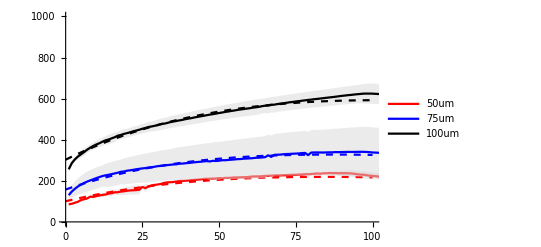

/media/xlei45/Extreme Pro/mathematica_code/result/sqrt50um75um100umLongTerm.png

{100.454+3.56135 x-0.0358653 x^2+0.000142044 x^3-2.44992×10^-7 x^4+1.54027×10^-10 x^5,157.66+5.22224 x-0.0559533 x^2+0.00025402 x^3-5.22854×10^-7 x^4+4.01963×10^-10 x^5,302.78+7.37047 x-0.0644722 x^2+0.00023259 x^3-3.75931×10^-7 x^4+2.25069×10^-10 x^5}

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";

filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
legends = {"50um", "75um", "100um"};
plots = {};
equations = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, 
   Transparent, Transparent, Black, Transparent}; (* List of colors *)

i = 1;
Do[
  files = FileNames[pattern, folder];
  data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
  data = DeleteCases[data, {}];
  minLength = Min[Length /@ data];
  truncatedData = Take[#, minLength] & /@ data;
  sqrtTruncatedData = Sqrt /@ truncatedData;
  meanData = Mean /@ Transpose[sqrtTruncatedData];
  stdData = StandardDeviation /@ Transpose[sqrtTruncatedData];
  upper = meanData + stdData;
  lower = meanData - stdData;
  (* fit a fourth degree polynomial model *)
  fit = Fit[meanData, {1, x, x^2,x^3,x^4,x^5}, x];
  (* keep the equation *)
  AppendTo[equations, fit];
  (* create plots for both the data and the fit *)
  plotData = ListLinePlot[{lower, meanData, upper}, 
        Filling -> {1 -> {3}}, 
        PlotStyle -> {colors[[i]], colors[[i + 1]], colors[[i + 2]]},
        FillingStyle -> Directive[Opacity[0.5], LightGray],
        FrameLabel -> {"Time (s)", "Sqrt Area (pixel)"},
        PlotRange -> {{0, 100}, {0, 1000}}];
  plotFit = Plot[fit, {x, 0, 100}, PlotStyle -> {colors[[i + 1]], Dashed}];
  (* append both plots to the list of plots *)
  AppendTo[plots, plotData];
  AppendTo[plots, plotFit];
  i = i + 3;, {pattern, filePatterns}] 

(* Create a combined plot with manually placed legend *)
combinedPlot = Legended[
      Show[plots],
      Placed[LineLegend[{Red, Blue, Black}, legends], Right]
  ]

Export[FileNameJoin[{resultFolder, "sqrt50um75um100umLongTerm.png"}], combinedPlot]

Print[equations]
```

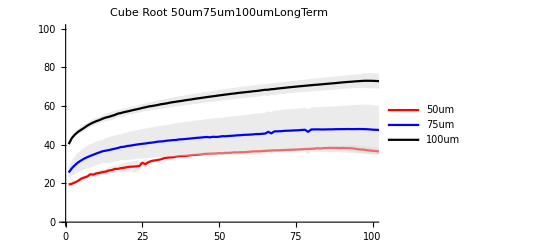

/media/xlei45/Extreme Pro/mathematica_code/result/cubeRoot50um75um100umLongTerm.png

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";

filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
legends = {"50um", "75um", "100um"};
plots = {};
colors = {Transparent, Red, Transparent, Transparent, Blue, Transparent, Transparent, Black, Transparent}; (* List of colors *)

i = 1;
Do[
 files = FileNames[pattern, folder];
 data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
 data = DeleteCases[data, {}];
 minLength = Min[Length /@ data];
 truncatedData = Take[#, minLength] & /@ data;
 cubeRootTruncatedData = CubeRoot /@ truncatedData;(*Change here*)
 meanData = Mean /@ Transpose[cubeRootTruncatedData];(*Change here*)
 stdData = StandardDeviation /@ Transpose[cubeRootTruncatedData];(*Change here*)
 upper = meanData + stdData;
 lower = meanData - stdData;
 plot = ListLinePlot[{lower, meanData, upper}, 
     Filling -> {1 -> {3}}, 
     PlotStyle -> {colors[[i]], colors[[i+1]], colors[[i+2]]}, (* Change color based on iteration *)
     FillingStyle -> Directive[Opacity[0.5], LightGray], 
     PlotLabel -> "Cube Root 50um75um100umLongTerm",(*Change here*)
     FrameLabel -> {"Time (s)", " Area (pixel^(1/3))"},(*Change here*)
     PlotRange -> {{0, 100}, {0, 100}}];
 AppendTo[plots, plot];
 i = i + 3;, {pattern, filePatterns}] (* Increment i by 3 at each iteration *)

(* Create a combined plot with manually placed legend *)
combinedPlot = Legended[
    Show[plots],
    Placed[LineLegend[{Red, Blue, Black}, legends], Right]
]

Export[FileNameJoin[{resultFolder, "cubeRoot50um75um100umLongTerm.png"}], combinedPlot] (* Export the plot with the legends *)
```

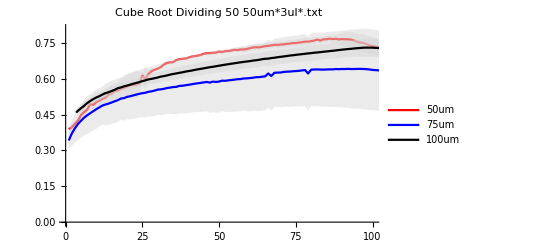

/media/xlei45/Extreme Pro/mathematica_code/result/cubeRootDividing50um75um100umLongTerm.png

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";
filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
plots = {};
dividers = {50, 75, 100};
legends = {"50um", "75um", "100um"};
colors = {Transparent, Red, Transparent, Transparent, Blue, Transparent, Transparent, Black, Transparent}; (* List of colors *)

i = 1;
Do[files = FileNames[pair[[1]], folder];
 data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
 data = DeleteCases[data, {}];
 minLength = Min[Length /@ data];
 truncatedData = Take[#, minLength] & /@ data;
 cubeRootTruncatedData = (CubeRoot[#]/pair[[2]]^(1)) & /@ truncatedData;
 meanData = Mean /@ Transpose[cubeRootTruncatedData];
 stdData = StandardDeviation /@ Transpose[cubeRootTruncatedData];
 upper = meanData + stdData;
 lower = meanData - stdData;
 plot = ListLinePlot[{lower, meanData, upper}, 
     Filling -> {1 -> {3}}, 
     PlotStyle -> {colors[[i]], colors[[i+1]], colors[[i+2]]}, (* Change color based on iteration *)
     FillingStyle -> Directive[Opacity[0.5], LightGray], 
     PlotLabel -> "Cube Root Dividing " <> ToString[pair[[2]]] <> " " <> pair[[1]], 
     FrameLabel -> {"Time (s)", " Area (pixel^(1/3))"}, 
     PlotRange -> {{0, 100}, Automatic}];  
 AppendTo[plots, plot];
 i = i + 3;, {pair, Transpose[{filePatterns, dividers}]}] (* Increment i by 3 at each iteration *)

(* Create a combined plot with manually placed legend *)
combinedPlot = Legended[
    Show[plots],
    Placed[LineLegend[{Red, Blue, Black}, legends], Right]
]

Export[FileNameJoin[{resultFolder, "cubeRootDividing50um75um100umLongTerm.png"}], combinedPlot] (* Export the plot with the legends *)
```

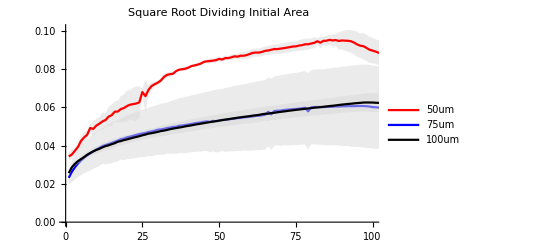

/media/xlei45/Extreme Pro/mathematica_code/result/squareRootDividing50um75um100umLongTerm.png

```mathematica
folder = "/media/xlei45/Extreme Pro/mathematica_code/data/prompt_long_pulse";
resultFolder = "/media/xlei45/Extreme Pro/mathematica_code/result";
filePatterns = {"50um*3ul*.txt", "75um*.txt", "100um*3ul*1ul*.txt"};
plots = {};
dividers = {50, 75, 100};
legends = {"50um", "75um", "100um"};
colors = {Transparent, Red, Transparent, Transparent, Blue, Transparent, Transparent, Black, Transparent}; (* List of colors *)

i = 1;
Do[files = FileNames[pair[[1]], folder];
 data = DeleteCases[#, 0] & /@ (ReadList[#, Number] & /@ files);
 data = DeleteCases[data, {}];
 minLength = Min[Length /@ data];
 truncatedData = Take[#, minLength] & /@ data;
 squareRootTruncatedData = (Sqrt[#]/pair[[2]]^(2)) & /@ truncatedData;
 meanData = Mean /@ Transpose[squareRootTruncatedData];
 stdData = StandardDeviation /@ Transpose[squareRootTruncatedData];
 upper = meanData + stdData;
 lower = meanData - stdData;
 plot = ListLinePlot[{lower, meanData, upper}, 
     Filling -> {1 -> {3}}, 
     PlotStyle -> {colors[[i]], colors[[i+1]], colors[[i+2]]}, (* Change color based on iteration *)
     FillingStyle -> Directive[Opacity[0.5], LightGray], 
     (*PlotLabel -> "Square Root Dividing " <> ToString[pair[[2]]] <> " " <> pair[[1]], *)
 PlotLabel -> "Square Root Dividing Initial Area", 
     FrameLabel -> {"Time (s)", " Area (pixel^(1/2))"}, 
     PlotRange -> {{0, 100}, Automatic}];
 AppendTo[plots, plot];
 i = i + 3;, {pair, Transpose[{filePatterns, dividers}]}] (* Increment i by 3 at each iteration *)

(* Create a combined plot with manually placed legend *)
combinedPlot = Legended[
    Show[plots],
    Placed[LineLegend[{Red, Blue, Black}, legends], Right]
]

Export[FileNameJoin[{resultFolder, "squareRootDividing50um75um100umLongTerm.png"}], combinedPlot] (* Export the plot with the legends *)
```

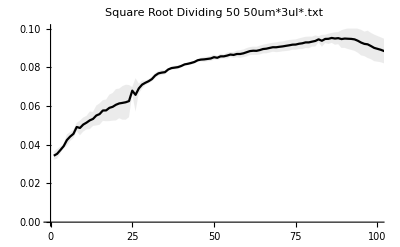

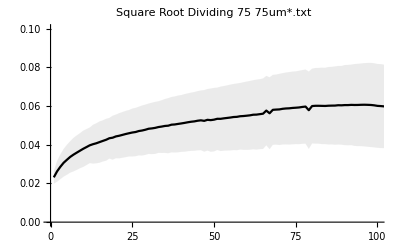

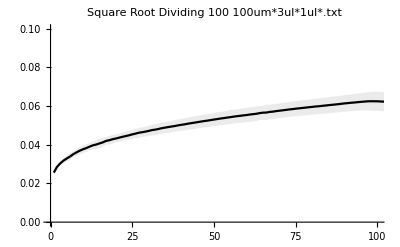

```mathematica
folder="F:\\mathematica_code\\data\\prompt_long_pulse";
resultFolder="F:\\mathematica_code\\result";
filePatterns={"50um*3ul*.txt","75um*.txt","100um*3ul*1ul*.txt"};
dividers={50,75,100};
Do[files=FileNames[pair[[1]],folder];
data=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files);
data=DeleteCases[data,{}];
minLength=Min[Length/@data];
truncatedData=Take[#,minLength]&/@data;
squareRootTruncatedData=(Sqrt[#]/pair[[2]]^(2))&/@truncatedData;
meanData=Mean/@Transpose[squareRootTruncatedData];
stdData=StandardDeviation/@Transpose[squareRootTruncatedData];
upper=meanData+stdData;
lower=meanData-stdData;
plot=ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Black,None},FillingStyle->Directive[Opacity[0.5],LightGray],PlotLabel->"Square Root Dividing "<>ToString[pair[[2]]]<>" "<>pair[[1]],FrameLabel->{"Time (s)"," Area (pixel^(1/2))"},PlotRange->{{0,100},{0,0.1}}];
Print[plot];(*Print the plot immediately*)Export[FileNameJoin[{resultFolder,"squareRootDividing"<>ToString[pair[[2]]]<>"umLongTerm.png"}],plot]  (*Export the plot to a separate file*),{pair,Transpose[{filePatterns,dividers}]}]
```

```mathematica
folder="F:\\mathematica_code\\data\\prompt_long_pulse";
resultFolder="F:\\mathematica_code\\result";
filePatterns={"50um*3ul*.txt","75um*.txt","100um*3ul*1ul*.txt"};
dividers={50,75,100};
Do[files=FileNames[pair[[1]],folder];
data=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files);
data=DeleteCases[data,{}];
minLength=Min[Length/@data];
truncatedData=Take[#,minLength]&/@data;
cubeRootTruncatedData=(CubeRoot[#]/pair[[2]]^(3))&/@truncatedData;
meanData=Mean/@Transpose[cubeRootTruncatedData];
stdData=StandardDeviation/@Transpose[cubeRootTruncatedData];
upper=meanData+stdData;
lower=meanData-stdData;
plot=ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Black,None},FillingStyle->Directive[Opacity[0.5],LightGray],PlotLabel->"Cube Root Dividing "<>ToString[pair[[2]]]<>"^3 "<>pair[[1]],FrameLabel->{"Time (s)"," Area (pixel^(1/3))"},PlotRange->{{0,100},Automatic}];
Show[plot];(*Display the plot*)Export[FileNameJoin[{resultFolder,"cubeRootDividing"<>ToString[pair[[2]]]<>"^3"<>StringReplace[pair[[1]],"*"->""]<>".png"}],plot];  (*Export the plot to a unique filename*),{pair,Transpose[{filePatterns,dividers}]}]
```

```mathematica
ClearAll
```

ClearAll

F:\mathematica_code\result\cubeRootDividing50um75um100umLongTerm.png

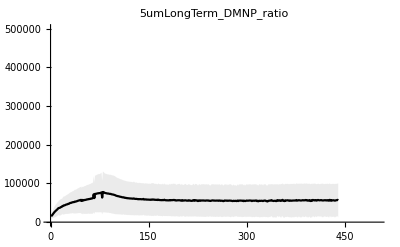

F:\mathematica_code\result\75umLongTerm_DMNP_ratio.png

```mathematica
folder="F:\\mathematica_code\\data\\prompt_long_pulse";
resultFolder="F:\\mathematica_code\\result";
filePatterns={"76um*3ul*1ul.txt","75um*6ul*.txt","75um*3ul*2ul*.txt"};
plots={};

Do[files=FileNames[pattern,folder];
data=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files);
data=DeleteCases[data,{}];
minLength=Min[Length/@data];
truncatedData=Take[#,minLength]&/@data;
meanData=Mean/@Transpose[truncatedData];
stdData=StandardDeviation/@Transpose[truncatedData];
upper=meanData+stdData;
lower=meanData-stdData;
plot=ListLinePlot[{lower,meanData,upper},Filling->{1->{3}},PlotStyle->{None,Black,None},FillingStyle->Directive[Opacity[0.5],LightGray],PlotLabel->"5umLongTerm_DMNP_ratio",FrameLabel->{"Time (s)"," Area (pixel^2)"},PlotRange->{{0,500},{0,500000}}];
AppendTo[plots,plot];,{pattern,filePatterns}]

Show[plots]
Export[FileNameJoin[{resultFolder,"75umLongTerm_DMNP_ratio.png"}],plots]
```

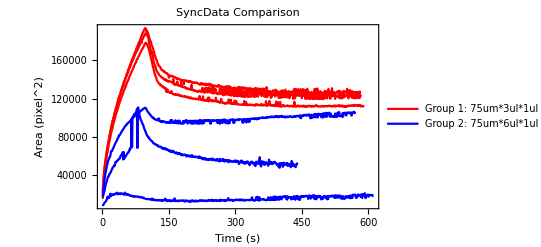

```mathematica
folder="F:\\mathematica_code\\data\\prompt_long_pulse";

(*Group 1*)
files1=FileNames["75um*3ul*1ul*.txt",folder];
syncData1=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files1);
syncData1=DeleteCases[syncData1,{}];

syncPlot1=ListPlot[syncData1,Joined->True,PlotStyle->Red,PlotLegends->{"Group 1: 75um*3ul*1ul"}];

(*Group 2*)
files2=FileNames["75um*6ul*1ul*.txt",folder];
syncData2=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files2);
syncData2=DeleteCases[syncData2,{}];

syncPlot2=ListPlot[syncData2,Joined->True,PlotStyle->Blue,PlotLegends->{"Group 2: 75um*6ul*1ul"}];

(*Group 3*)
files3=FileNames["75um*3ul*2ul*.txt",folder];
syncData3=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files3);
syncData3=DeleteCases[syncData3,{}];

syncPlot3=ListPlot[syncData3,Joined->True,PlotStyle->Black,PlotLegends->{"Group 3: 75um*3ul*2ul"}];

(*Combine plots*)
Show[syncPlot1,syncPlot2,syncPlot3,PlotLabel->"75umLongTerm_DMNP_ratio",FrameLabel->{"Time (s)","Area (pixel^2)"},PlotRange->All]
```

```mathematica
folder="F:\\mathematica_code\\data\\prompt_long_pulse";
resultFolder="F:\\mathematica_code\\result";

(*Group 1*)
files1=FileNames["75um*3ul*1ul*.txt",folder];
syncData1=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files1);
syncData1=DeleteCases[syncData1,{}];

syncPlot1=ListPlot[syncData1,Joined->True,PlotStyle->Red,PlotLegends->{"Group 1: 75um*3ul_Tcb2*1ul_DMNP"}];

(*Group 2*)
files2=FileNames["75um*6ul*1ul*.txt",folder];
syncData2=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files2);
syncData2=DeleteCases[syncData2,{}];

syncPlot2=ListPlot[syncData2,Joined->True,PlotStyle->Blue,PlotLegends->{"Group 2: 75um*6ul_Tcb2*1ul_DMNP"}];

(*Group 3*)
files3=FileNames["75um*3ul*2ul*.txt",folder];
syncData3=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files3);
syncData3=DeleteCases[syncData3,{}];

syncPlot3=ListPlot[syncData3,Joined->True,PlotStyle->Black,PlotLegends->{"Group 3: 75um*3ul_Tcb2*2ul_DMNP"}];

(*Combine plots*)
combinedPlot=Show[syncPlot1,syncPlot2,syncPlot3,PlotLabel->"75umLongTerm_DMNP_ratio",FrameLabel->{"Time (s)","Area (pixel^2)"},PlotRange->All];

exportPath=FileNameJoin[{resultFolder,"75umLongTerm_DMNP_ratio.png"}];
Export[exportPath,combinedPlot];
```

```mathematica
folder="F:\\mathematica_code\\data\\prompt_long_pulse";
resultFolder="F:\\mathematica_code\\result";

(*Group 1*)
files1=FileNames["50um*3ul*1ul*.txt",folder];
syncData1=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files1);
syncData1=DeleteCases[syncData1,{}];

syncPlot1=ListPlot[syncData1,Joined->True,PlotStyle->Red,PlotLegends->{"Group 1: 50um*3ul_Tcb2*1ul_DMNP"}];

(*Group 2*)
files2=FileNames["50um*6ul*1ul*.txt",folder];
syncData2=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files2);
syncData2=DeleteCases[syncData2,{}];

syncPlot2=ListPlot[syncData2,Joined->True,PlotStyle->Blue,PlotLegends->{"Group 2: 50um*6ul_Tcb2*1ul_DMNP"}];

(*Group 3*)
files3=FileNames["50um*3ul*2ul*.txt",folder];
syncData3=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files3);
syncData3=DeleteCases[syncData3,{}];

syncPlot3=ListPlot[syncData3,Joined->True,PlotStyle->Black,PlotLegends->{"Group 3: 50um*3ul_Tcb2*2ul_DMNP"}];

(*Combine plots*)
combinedPlot=Show[syncPlot1,syncPlot2,syncPlot3,PlotLabel->"50umLongTerm_DMNP_ratio",FrameLabel->{"Time (s)","Area (pixel^2)"},PlotRange->All];

exportPath=FileNameJoin[{resultFolder,"50umLongTerm_DMNP_ratio.png"}];
Export[exportPath,combinedPlot];
```

```mathematica
folder="F:\\mathematica_code\\data\\prompt_long_pulse";
resultFolder="F:\\mathematica_code\\result";

(*Group 1*)
files1=FileNames["100um*3ul*1ul*.txt",folder];
syncData1=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files1);
syncData1=DeleteCases[syncData1,{}];

syncPlot1=ListPlot[syncData1,Joined->True,PlotStyle->Red,PlotLegends->{"Group 1: 100um*3ul_Tcb2*1ul_DMNP"},PlotRange->{{0,600},{0,8000000}}];

(*Group 2*)
files2=FileNames["100um*6ul*1ul*.txt",folder];
syncData2=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files2);
syncData2=DeleteCases[syncData2,{}];

syncPlot2=ListPlot[syncData2,Joined->True,PlotStyle->Blue,PlotLegends->{"Group 2: 100um*6ul_Tcb2*1ul_DMNP"},PlotRange->{{0,600},{0,8000000}}];

(*Group 3*)
files3=FileNames["100um*3ul*2ul*.txt",folder];
syncData3=DeleteCases[#,0]&/@(ReadList[#,Number]&/@files3);
syncData3=DeleteCases[syncData3,{}];

syncPlot3=ListPlot[syncData3,Joined->True,PlotStyle->Black,PlotLegends->{"Group 3: 100um*3ul_Tcb2*2ul_DMNP"},PlotRange->{{0,600},{0,8000000}}];

(*Combine plots*)
combinedPlot=Show[syncPlot1,syncPlot2,syncPlot3,PlotLabel->"100umLongTerm_DMNP_ratio",FrameLabel->{"Time (s)","Area (pixel^2)"},PlotRange->All];

exportPath=FileNameJoin[{resultFolder,"100umLongTerm_DMNP_ratio.png"}];
Export[exportPath,combinedPlot];
```